## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="GND";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_GND_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{nadp,Null;6pgc,Null,Keq substrate}

{0.0123,Keq value}

{6pgc,Km or S05 substrate}

{0.000093,Km or S05 value}

{nadp,Km or S05 substrate}

{0.000049,Km or S05 value}

{{{6pgc,Null}},kcat substrates}

{10.23,kcat value}

{{{nadp,Null}},kcat substrates}

{21.07,kcat value}

((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND

ordered sequential; [6pgc,nadp,co2,nadph,ru5p__D]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp,Null;6pgc,Null | 0.0123 | 0.011685
0.012915 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 6pgc | 0.000093 | 0.00092
0.000094 | nadp | 0.002 | M | 8 | 25 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04
1 | nadp | 0.000049 | 0.000042
0.000056 | 6pgc | 0.002 | M | 8 | 25 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 6pgc | Null | 30.7188 | 29.1828
32.2547 | 1/s | 8 | 37 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04
1 | nadp | Null | 63.2692 | 60.1058
66.4327 | 1/s | 8 | 37 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND

ordered sequential; [6pgc,nadp,co2,nadph,ru5p__D]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp,Null;6pgc,Null | 0.0123 | 0.011685
0.012915 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 6pgc | 0.000093 | 0.00092
0.000094 | nadp | 0.002 | M | 8 | 25 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04
1 | nadp | 0.000049 | 0.000042
0.000056 | 6pgc | 0.002 | M | 8 | 25 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 6pgc | Null | 30.7188 | 29.1828
32.2547 | 1/s | 8 | 37 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04
1 | nadp | Null | 63.2692 | 60.1058
66.4327 | 1/s | 8 | 37 | trishcl | 0.05 | mg2 | 0.02
cl | 0.04

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_GND[c] + 6pgc[c] <=> E_GND[c]&6pgc",
				"E_GND[c]&6pgc + nadp[c] <=> E_GND[c]&6pgc&nadp",
				"E_GND[c]&6pgc&nadp <=> E_GND[c]&ru5p__D&nadph&co2",
				"E_GND[c]&ru5p__D&nadph&co2 <=> E_GND[c]&ru5p__D&nadph + co2[c]",
				"E_GND[c]&ru5p__D&nadph <=> E_GND[c]&ru5p__D + nadph[c]",
				"E_GND[c]&ru5p__D <=> E_GND[c] + ru5p__D[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GND^c)_^+(6pgc)^c⇌(GND^c&(6pgc)^c)_^)^GND1,((GND^c&ru5p_^D)_^⇌(GND^c)_^+ru5p__D^c)^GND2,((GND^c&(6pgc)^c)_^+nadp^c⇌(GND^c&(6pgc)^c&nadp^c)_^)^GND3,((GND^c&ru5p_^D&nadph^c)_^⇌(GND^c&ru5p_^D)_^+nadph^c)^GND4,((GND^c&(6pgc)^c&nadp^c)_^⇌(GND^c&ru5p_^D&nadph^c&co2^c)_^)^GND5,((GND^c&ru5p_^D&nadph^c&co2^c)_^⇌(GND^c&ru5p_^D&nadph^c)_^+co2^c)^GND6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((GND^c)_^+(6pgc)^c⇌(GND^c&(6pgc)^c)_^)^GND1,Overscript[(GND^c&ru5p_^D)_^⇌(GND^c)_^+ru5p__D^c, GND2],((GND^c&(6pgc)^c)_^+nadp^c⇌(GND^c&(6pgc)^c&nadp^c)_^)^GND3,Overscript[(GND^c&ru5p_^D&nadph^c)_^⇌(GND^c&ru5p_^D)_^+nadph^c, GND4],((GND^c&(6pgc)^c&nadp^c)_^⇌(GND^c&ru5p_^D&nadph^c&co2^c)_^)^GND5,Overscript[(GND^c&ru5p_^D&nadph^c&co2^c)_^⇌(GND^c&ru5p_^D&nadph^c)_^+co2^c, GND6]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{(6pgc)^c→0,nadp^c→0}

{co2^c→0,nadph^c→0,ru5p__D^c→0}

{(6pgc)^c→∞,nadp^c→∞}

{co2^c→∞,nadph^c→∞,ru5p__D^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((GND^c&(6pgc)^c&nadp^c)_^-((GND^c&ru5p_^D&nadph^c&co2^c)_^)/K_GND5) Volume_c k_GND5^⟶}

Volume_c (-(GND^c&ru5p_^D&nadph^c&co2^c)_^ k_GND5^⟵+(GND^c&(6pgc)^c&nadp^c)_^ k_GND5^⟶)

1

2

3

1.17662

4

0.00176

5

0.00018

Simplifying...

6

0.467659

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	6pgc[c]	co2[c]	nadp[c]	nadph[c]	ru5p__D[c]	param_GND_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt"	0.0123
1	9.299999999999994e-6	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.09090909090909086
1	0.00001473950668988835	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.13680688860320997
1	0.000023360543813039098	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.20076000891310178
1	0.00003702396686147526	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.2847472489508015
1	0.00005867903303665791	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.38686317984685675
1	0.00009299999999999993	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.49999999999999983
1	0.0001473950668988835	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.613136820153143
1	0.00023360543813039097	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.7152527510491987
1	0.00037023966861475223	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.7992399910868982
1	0.000586790330366579	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.8631931113967899
1	0.0009299999999999993	0	0.002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt"	0.909090909090909
1	0.002	0	4.900000000000002e-6	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.09090909090909094
1	0.002	0	7.765976643059462e-6	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.13680688860321008
1	0.002	0	0.000012308243514396957	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.20076000891310197
1	0.002	0	0.000019507251357121357	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.28474724895080133
1	0.002	0	0.00003091690987952947	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.3868631798468569
1	0.002	0	0.00004900000000000002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.5000000000000001
1	0.002	0	0.00007765976643059463	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.6131368201531433
1	0.002	0	0.00012308243514396957	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.7152527510491988
1	0.002	0	0.0001950725135712138	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.7992399910868984
1	0.002	0	0.0003091690987952947	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.86319311139679
1	0.002	0	0.0004900000000000002	0	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt"	0.9090909090909092
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	30.718757399075113
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905
1	0.01	0	0.01	0	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt"	63.269229559971905

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateRev_co2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateRev_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateRev_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateRev_co2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateRev_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateRev_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.01149522279
best_fit: 1.01001650703
best_fit: 1.08491631878
best_fit: 0.765906347163
best_fit: 1.02104557519

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | relRateFor_6pgc | 1.38078×10^-11 | 1.90657×10^-22 | 2.89035×10^-12 | 3.17939×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_6pgc | 1.31108×10^-11 | 1.71894×10^-22 | 4.13003×10^-12 | 3.01888×10^-9 | 0.136807 | 0.136807
1 | relRateFor_6pgc | 1.21396×10^-11 | 1.4737×10^-22 | 5.61171×10^-12 | 2.79523×10^-9 | 0.20076 | 0.20076
1 | relRateFor_6pgc | 1.08639×10^-11 | 1.18024×10^-22 | 7.12291×10^-12 | 2.50149×10^-9 | 0.284747 | 0.284747
1 | relRateFor_6pgc | 9.31294×10^-12 | 8.67308×10^-23 | 8.29581×10^-12 | 2.14438×10^-9 | 0.386863 | 0.386863
1 | relRateFor_6pgc | 7.59437×10^-12 | 5.76744×10^-23 | 8.74339×10^-12 | 1.74868×10^-9 | 0.5 | 0.5
1 | relRateFor_6pgc | 5.87597×10^-12 | 3.4527×10^-23 | 8.2957×10^-12 | 1.35299×10^-9 | 0.613137 | 0.613137
1 | relRateFor_6pgc | 4.32507×10^-12 | 1.87062×10^-23 | 7.12308×10^-12 | 9.95883×10^-10 | 0.715253 | 0.715253
1 | relRateFor_6pgc | 3.04927×10^-12 | 9.29804×10^-24 | 5.61162×10^-12 | 7.0212×10^-10 | 0.79924 | 0.79924
1 | relRateFor_6pgc | 2.07798×10^-12 | 4.31799×10^-24 | 4.13014×10^-12 | 4.78472×10^-10 | 0.863193 | 0.863193
1 | relRateFor_6pgc | 1.38074×10^-12 | 1.90645×10^-24 | 2.89024×10^-12 | 3.17927×10^-10 | 0.909091 | 0.909091
1 | relRateFor_nadp | 3.05955×10^-12 | 9.36086×10^-24 | 6.4046×10^-13 | 7.04506×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_nadp | 2.90501×10^-12 | 8.43908×10^-24 | 9.15129×10^-13 | 6.6892×10^-10 | 0.136807 | 0.136807
1 | relRateFor_nadp | 2.68985×10^-12 | 7.23528×10^-24 | 1.24339×10^-12 | 6.19344×10^-10 | 0.20076 | 0.20076
1 | relRateFor_nadp | 2.4073×10^-12 | 5.79508×10^-24 | 1.57835×10^-12 | 5.54298×10^-10 | 0.284747 | 0.284747
1 | relRateFor_nadp | 2.06363×10^-12 | 4.25856×10^-24 | 1.83825×10^-12 | 4.75168×10^-10 | 0.386863 | 0.386863
1 | relRateFor_nadp | 1.68277×10^-12 | 2.8317×10^-24 | 1.93734×10^-12 | 3.87468×10^-10 | 0.5 | 0.5
1 | relRateFor_nadp | 1.30196×10^-12 | 1.6951×10^-24 | 1.83809×10^-12 | 2.99784×10^-10 | 0.613137 | 0.613137
1 | relRateFor_nadp | 9.584×10^-13 | 9.18531×10^-25 | 1.5784×10^-12 | 2.20678×10^-10 | 0.715253 | 0.715253
1 | relRateFor_nadp | 6.75668×10^-13 | 4.56527×10^-25 | 1.24345×10^-12 | 1.55579×10^-10 | 0.79924 | 0.79924
1 | relRateFor_nadp | 4.60451×10^-13 | 2.12015×10^-25 | 9.15157×10^-13 | 1.0602×10^-10 | 0.863193 | 0.863193
1 | relRateFor_nadp | 3.05977×10^-13 | 9.36222×10^-26 | 6.40488×10^-13 | 7.04536×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857

### Simulated Data and Best Fit Data Plot

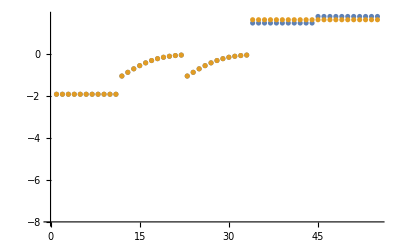

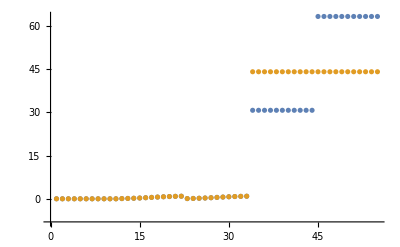

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

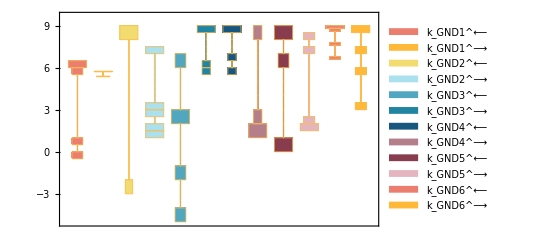

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

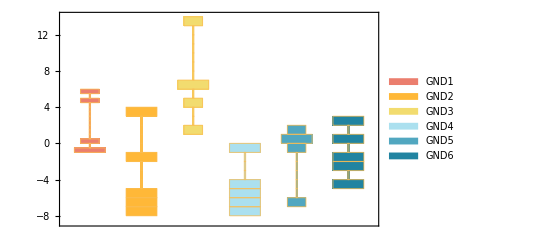

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

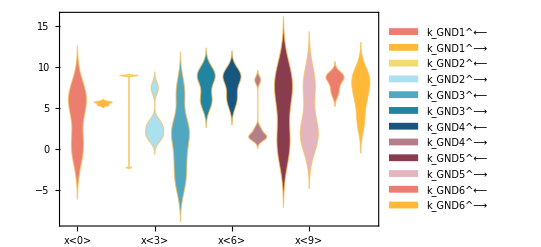

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

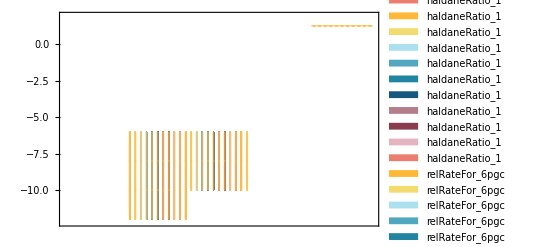

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,{{1,6pgc,0.000093,{0.00092,0.000094},{{nadp,0.002}},M,8,25,{{trishcl,0.05}},{{mg2,0.02},{cl,0.04}}},{1,nadp,0.000049,{0.000042,0.000056},{{6pgc,0.002}},M,8,25,{{trishcl,0.05}},{{mg2,0.02},{cl,0.04}}}},{((6pgc)^c k_GND1^⟶ (nadp^c k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ (k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶)+nadp^c k_GND3^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶)))))/(nadp^c k_GND2^⟶ k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND1^⟵ k_GND2^⟶ k_GND4^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+k_GND6^⟶))+(6pgc)^c k_GND1^⟶ (nadp^c k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ (k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶)+nadp^c k_GND3^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶))))),(nadp^c k_GND3^⟶ (k_GND2^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+(6pgc)^c k_GND1^⟶ (k_GND2^⟶ k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶))))/(nadp^c k_GND2^⟶ k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND1^⟵ k_GND2^⟶ k_GND4^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+k_GND6^⟶))+(6pgc)^c k_GND1^⟶ (nadp^c k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ (k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶)+nadp^c k_GND3^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶)))))},{(co2^c (k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) k_GND3^⟵ k_GND5^⟵+nadph^c k_GND4^⟵ (k_GND1^⟵ k_GND3^⟵ k_GND5^⟵+ru5p__D^c k_GND2^⟵ (k_GND3^⟵ k_GND5^⟵+k_GND1^⟵ (k_GND3^⟵+k_GND5^⟵+k_GND5^⟶)))) k_GND6^⟵)/(k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶))))),(nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶)))))/(k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶))))),(ru5p__D^c k_GND2^⟵ (co2^c nadph^c k_GND3^⟵ k_GND4^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND1^⟵ k_GND3^⟵ (co2^c k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND1^⟵ k_GND4^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶))))/(k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶)))))},{(6pgc)^c→∞,nadp^c→∞},{co2^c→∞,nadph^c→∞,ru5p__D^c→∞},{k_GND1^⟵→5.83733,k_GND1^⟶→236077.,k_GND2^⟵→7.78217×10^8,k_GND2^⟶→51.3768,k_GND3^⟵→103.251,k_GND3^⟶→1.56697×10^6,k_GND4^⟵→6.62102×10^8,k_GND4^⟶→2.61338×10^8,k_GND5^⟵→1.81229,k_GND5^⟶→40.4979,k_GND6^⟵→5.43416×10^7,k_GND6^⟶→1870.18},1,GND]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
30.7188 | (7.52369×10^26 nadp^c)/(2.10851×10^16+1.59348×10^21 nadp^c+236077. (3.10156×10^19 nadp^c+51.3768 (7.03063×10^13+7.83183×10^17 nadp^c))) | 3.25534 Abs[30.7188-(7.52369×10^26 nadp^c)/(2.10851×10^16+1.59348×10^21 nadp^c+236077. (3.10156×10^19 nadp^c+51.3768 (7.03063×10^13+7.83183×10^17 nadp^c)))]
63.2692 | (7.52369×10^26 (6pgc)^c)/(1.5935×10^21+1.68221×10^25 (6pgc)^c) | 1.58055 Abs[63.2692-(7.52369×10^26 (6pgc)^c)/(1.5935×10^21+1.68221×10^25 (6pgc)^c)]

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.0123 | 0.0123 | 0.000179966

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.0123 | 0.0123 | 0.000179966

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,9.3×10^-6,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.0909091},{1,0.0000147395,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.136807},{1,0.0000233605,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.20076},{1,0.000037024,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.284747},{1,0.000058679,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.386863},{1,0.000093,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.5},{1,0.000147395,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.613137},{1,0.000233605,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.715253},{1,0.00037024,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.79924},{1,0.00058679,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.863193},{1,0.00093,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.909091},{1,0.002,0,4.9×10^-6,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.0909091},{1,0.002,0,7.76598×10^-6,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.136807},{1,0.002,0,0.0000123082,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.20076},{1,0.002,0,0.0000195073,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.284747},{1,0.002,0,0.0000309169,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.386863},{1,0.002,0,0.000049,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.5},{1,0.002,0,0.0000776598,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.613137},{1,0.002,0,0.000123082,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.715253},{1,0.002,0,0.000195073,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.79924},{1,0.002,0,0.000309169,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.863193},{1,0.002,0,0.00049,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.909091},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692}},{0.541549,{5.83733,236077.,7.78217×10^8,51.3768,103.251,1.56697×10^6,6.62102×10^8,2.61338×10^8,1.81229,40.4979,5.43416×10^7,1870.18},{0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857}},{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.000437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.000694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.00437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.00694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.}},{1.15461×10^-22,{538.263,26248.2,1.50533×10^8,28.8607,194.069,9.19561×10^6},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.}},{Priority,r5p[c],ru5p__D[c],param_RPIb_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,GND,«20»,{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]